# Spring with drift

## Free-space solution starting at x0 > 0, traveling to the left at speed v.

```mathematica
p[x, t] = Sqrt[k/(2*Pi*d)]*Exp[-k/(2*d) * (x-x0+v*t)^2]
```

(ⅇ^(-(k (t v+x-x0)^2)/(2 d)) √(k/d))/(√(2 π))

```mathematica
Integrate[p[x, t], {x, -Infinity, Infinity}]
```

$Aborted

## Find absorption probability q(absorbed at t | survived until t)

```mathematica
q[t] =Normal @ FullSimplify[Integrate[p[x,t], {x, -Infinity, 0}]]
```

1/2 (1+Erf[(√(k/d) (t v-x0))/(√2)])

```mathematica
q[t_, x0_, v_, d_, k_] = q[t]
```

1/2 (1+Erf[(√(k/d) (t v-x0))/(√2)])

```mathematica
Manipulate[Plot[q[t, x0, v, D, k], {t, -1000, 1000}, PlotRange->{0, 1}], {k, 1, 1}, {D, 2,2}, {v, 0,0.1}, {x0, 1, 5}]
```

D$$::shdw: Symbol D$$ appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

## Integrate to get survival probability from dS/S = -q(t) S(t)

```mathematica
lnS[t] = FullSimplify[-Integrate[q[t], t]]
```

1/2 (-2 t-(ⅇ^(-(k (-t v+x0)^2)/(2 d)) √(2/π))/(√(k/d) v)+(√d √(k/d) x0 Erf[(√k (t v-x0))/(√2 √d)])/(√k v)+t Erfc[(√(k/d) (t v-x0))/(√2)])

```mathematica
S[t] = FullSimplify[Exp[lnS[t]]]
```

ⅇ^(-(ⅇ^(-(k (-t v+x0)^2)/(2 d)))/(√(k/d) √(2 π) v)+(√d √(k/d) x0 Erf[(√k (t v-x0))/(√2 √d)])/(2 √k v)-1/2 t (1+Erf[(√(k/d) (t v-x0))/(√2)]))

Apply initial condition

```mathematica
S0 = Exp[(x0/(2*v))*Erf[Sqrt[k/(2*d)]*x0]]*Exp[(1/v)*Sqrt[d/(2*Pi*k)]*Exp[-k/(2*d)*x0^2]]
```

ⅇ^((ⅇ^(-(k x0^2)/(2 d)) √(d/k))/(√(2 π) v)+(x0 Erf[(√(k/d) x0)/(√2)])/(2 v))

```mathematica
S[t] = S0*S[t]
```

ⅇ^((ⅇ^(-(k x0^2)/(2 d)) √(d/k))/(√(2 π) v)-(ⅇ^(-(k (-t v+x0)^2)/(2 d)))/(√(k/d) √(2 π) v)+(√d √(k/d) x0 Erf[(√k (t v-x0))/(√2 √d)])/(2 √k v)-1/2 t (1+Erf[(√(k/d) (t v-x0))/(√2)])+(x0 Erf[(√(k/d) x0)/(√2)])/(2 v))

## Get first-passage time probability

```mathematica
f[t_, x0_, v_, d_, k_] =S[t]*q[t]
```

1/2 ⅇ^((ⅇ^(-(k x0^2)/(2 d)) √(d/k))/(√(2 π) v)-(ⅇ^(-(k (-t v+x0)^2)/(2 d)))/(√(k/d) √(2 π) v)+(√d √(k/d) x0 Erf[(√k (t v-x0))/(√2 √d)])/(2 √k v)-1/2 t (1+Erf[(√(k/d) (t v-x0))/(√2)])+(x0 Erf[(√(k/d) x0)/(√2)])/(2 v)) (1+Erf[(√(k/d) (t v-x0))/(√2)])

```mathematica
S[t_, x0_, v_, d_, k_] = S[t]
```

ⅇ^((ⅇ^(-(k x0^2)/(2 d)) √(d/k))/(√(2 π) v)-(ⅇ^(-(k (-t v+x0)^2)/(2 d)))/(√(k/d) √(2 π) v)+(√d √(k/d) x0 Erf[(√k (t v-x0))/(√2 √d)])/(2 √k v)-1/2 t (1+Erf[(√(k/d) (t v-x0))/(√2)])+(x0 Erf[(√(k/d) x0)/(√2)])/(2 v))

## Plots and scaling

## Behavior with v near crossover

2

0.00935547

{0.01215,0.00405,0.00135,0.00045,0.00015,0.00005}

0.5

1

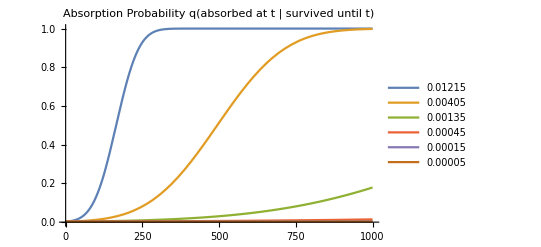

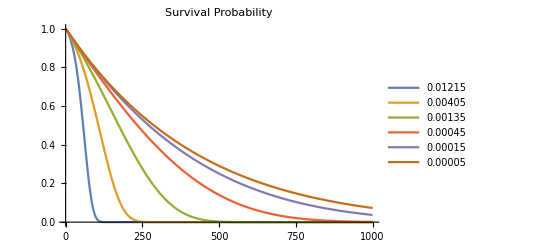

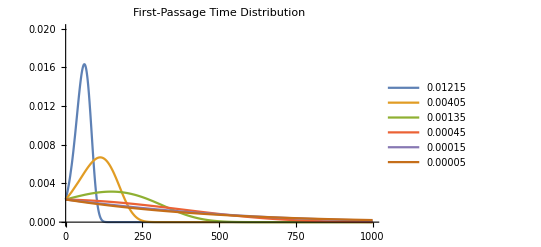

```mathematica
x0Constant = 2
vCrossover = N[Erfc[x0Constant]]*x0Constant
vRange = Reverse[N[PowerRange[5*^-5,2*^-2 , 3]]]
 DConstant = 0.5
 kConstant = 1

Plot[Evaluate[q[t,x0Constant, #, DConstant, kConstant]&/@vRange],{t,0,1000}, PlotRange->{0,1}, PlotLegends->vRange, PlotLabel->"Absorption Probability q(absorbed at t | survived until t)"]
Plot[Evaluate[S[t,x0Constant, #, DConstant, kConstant]&/@vRange],{t,0,1000}, PlotRange->{0,1}, PlotLegends->vRange, PlotLabel->"Survival Probability"]
Plot[Evaluate[f[t,x0Constant, #, DConstant, kConstant]&/@vRange],{t,0,1000}, PlotRange->{0,0.02}, PlotLegends->vRange, PlotLabel->"First-Passage Time Distribution"]
```

## Behavior with x0 near crossover

{1,2,3,4,5,6,7}

1/1000

{x→2.50348}

0.5

1

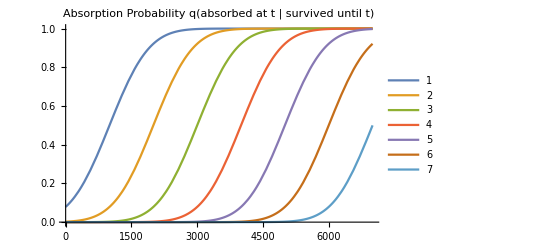

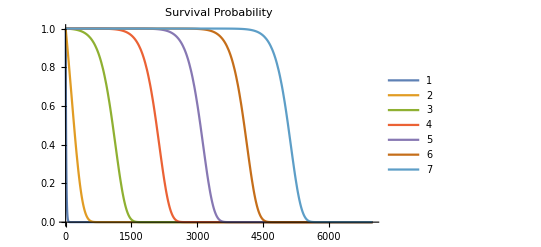

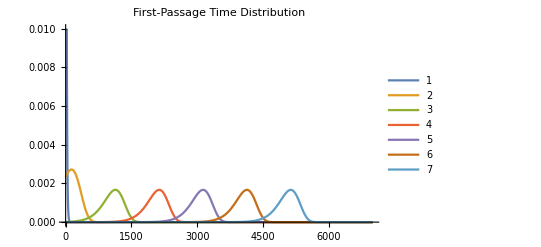

```mathematica
x0Range = Range[1, 7, 1]
vConstant = 1*^-3
x0Crossover = FindRoot[vConstant - x*(1-Erf[x]), {x, 2}]
 DConstant = 0.5
 kConstant = 1

Plot[Evaluate[q[t,#, vConstant, DConstant, kConstant]&/@x0Range],{t,0,7000}, PlotRange->{0,1}, PlotLegends->x0Range, PlotLabel->"Absorption Probability q(absorbed at t | survived until t)"]
Plot[Evaluate[S[t,#, vConstant, DConstant, kConstant]&/@x0Range],{t,0,7000}, PlotRange->{0,1}, PlotLegends->x0Range, PlotLabel->"Survival Probability"]
Plot[Evaluate[f[t,#, vConstant, DConstant, kConstant]&/@x0Range],{t,0,7000}, PlotRange->{0,0.01}, PlotLegends->x0Range, PlotLabel->"First-Passage Time Distribution"]
```

### Drift-dominated scaling

#### MFPT and variance with x0

```mathematica
x0Range = PowerRange[10, 100, 1.25]
vConstant = 1*^-2
 DConstant = 0.5
 kConstant = 1
```

{10.,12.5,15.625,19.5313,24.4141,30.5176,38.147,47.6837,59.6046,74.5058,93.1323}

1/100

0.5

1

```mathematica
x0means = NIntegrate[t*f[t,x0Range, vConstant, DConstant, kConstant], {t, 0, 12000}]
x0meansP =  x0Range/vConstant
x0meansP - x0means
x0var = NIntegrate[t*t*f[t,x0Range, vConstant, DConstant, kConstant], {t, 0, 12000}] - x0means^2
(*x0varP =  DConstant/(kConstant*vConstant^2)*)
```

{859.067,1109.07,1421.57,1812.19,2300.47,2910.83,3673.76,4627.44,5819.53,7309.65,9172.29}

{1000.,1250.,1562.5,1953.13,2441.41,3051.76,3814.7,4768.37,5960.46,7450.58,9313.23}

{140.933,140.933,140.933,140.933,140.933,140.933,140.933,140.933,140.933,140.933,140.933}

{1036.68,1036.68,1036.68,1036.68,1036.68,1036.68,1036.68,1036.68,1036.68,1036.68,1036.68}

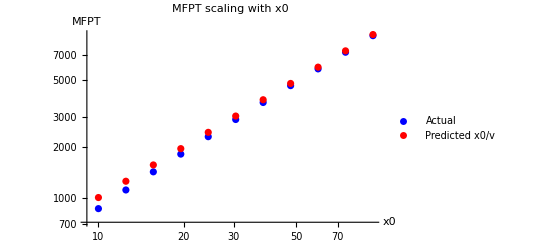

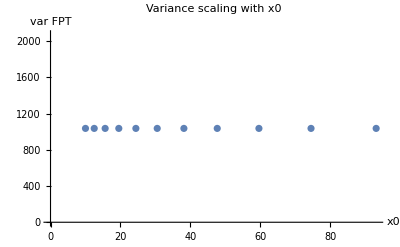

```mathematica
ListLogLogPlot[{Thread[{x0Range, x0means}], Thread[{x0Range, x0meansP}]}, AxesLabel->{"x0", "MFPT"}, PlotLabel->"MFPT scaling with x0", PlotLegends->{"Actual", "Predicted x0/v"}, PlotStyle->{Blue, Red}]
ListPlot[Thread[{x0Range, x0var}], AxesLabel->{"x0", "var FPT"}, PlotLabel->"Variance scaling with x0"]
```

#### MFPT and variance with v

```mathematica
vRange = N[PowerRange[2*^-4,5*^-2 , 2]]
 DConstant = 0.5
 kConstant = 1
x0Constant = 10
```

{0.0002,0.0004,0.0008,0.0016,0.0032,0.0064,0.0128,0.0256}

0.5

1

10

```mathematica
vmeans = NIntegrate[t*f[t,x0Constant, vRange, DConstant, kConstant], {t, 0, 50000}]
vvar = NIntegrate[t*t*f[t,x0Constant, vRange, DConstant, kConstant], {t, 0,50000}]  - vmeans^2
```

{38586.7,19631.,9992.94,5090.15,2594.83,1324.04,676.409,346.075}

{1.37464×10^6,375393.,103335.,28717.7,8074.07,2303.07,669.176,199.255}

{{0.0002,38586.7},{0.0004,19631.},{0.0008,9992.94},{0.0016,5090.15},{0.0032,2594.83},{0.0064,1324.04},{0.0128,676.409},{0.0256,346.075}}

{{0.0002,1.37464×10^6},{0.0004,375393.},{0.0008,103335.},{0.0016,28717.7},{0.0032,8074.07},{0.0064,2303.07},{0.0128,669.176},{0.0256,199.255}}

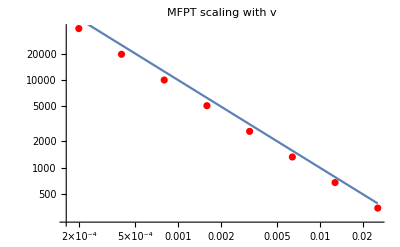

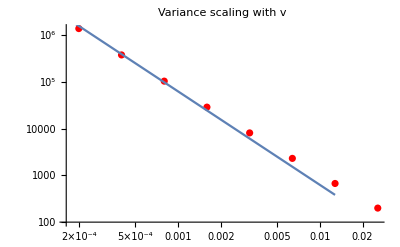

```mathematica
meandata = Thread[{vRange, vmeans}]
vardata = Thread[{vRange, vvar}] 
Show[ListLogLogPlot[meandata,PlotStyle->Red, PlotLabel->"MFPT scaling with v"], LogLogPlot[x0Constant/v, {v, 0, 0.0256}, PlotLegends->"Slope = -1"]]
Show[ListLogLogPlot[vardata,PlotStyle->Red, PlotLabel->"Variance scaling with v"], LogLogPlot[DConstant/(8*kConstant*x^2), {x, 0, 0.0128}, PlotLegends->"Slope = -2"]]
```

#### MFPT and variance with D/κ (let κ be fixed at 1)

```mathematica
vConstant = 0.01
 DRange = PowerRange[0.1, 45, 2.7]
 kConstant = 1
x0Constant = 15
```

0.01

{0.1,0.27,0.729,1.9683,5.31441,14.3489,38.742}

1

15

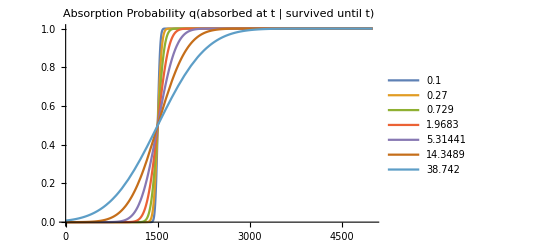

General::munfl: Exp[-1125.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1124.85] is too small to represent as a normalized machine number; precision may be lost.

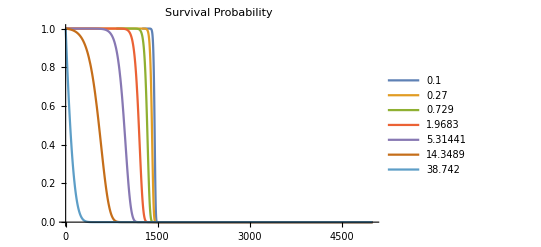

General::munfl: Exp[-1125.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1124.95] is too small to represent as a normalized machine number; precision may be lost.

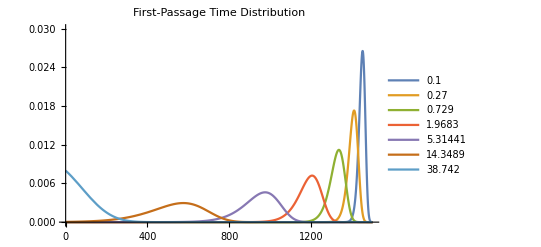

```mathematica
Plot[Evaluate[q[t,x0Constant, vConstant, #, kConstant]&/@DRange],{t,0,5000}, PlotRange->{0,1}, PlotLegends->DRange, PlotLabel->"Absorption Probability q(absorbed at t | survived until t)"]
Plot[Evaluate[S[t,x0Constant, vConstant, #, kConstant]&/@DRange],{t,0,5000}, PlotRange->{0,1}, PlotLegends->DRange, PlotLabel->"Survival Probability"]
Plot[Evaluate[f[t,x0Constant, vConstant, #, kConstant]&/@DRange],{t ,0, 1500}, PlotRange->{0,0.03}, PlotLegends->DRange, PlotLabel->"First-Passage Time Distribution"]
```

```mathematica
Dmeans = NIntegrate[t*f[t,x0Constant, vConstant, DRange, kConstant], {t, 8000, 11000}]
Dvar = NIntegrate[t*t*f[t,x0Constant, vConstant, DRange, kConstant], {t, 8000,11000}]  - Dmeans^2
```

{9988.66,9982.15,9972.52,9958.36,9937.68,9907.62,9864.09,9801.31,9711.04,9581.62,9396.51}

{36.0398,61.1904,105.003,181.784,317.051,556.476,982.041,1741.28,3100.49,5541.07,9935.52}

{{0.01,9988.66},{0.019,9982.15},{0.0361,9972.52},{0.06859,9958.36},{0.130321,9937.68},{0.24761,9907.62},{0.470459,9864.09},{0.893872,9801.31},{1.69836,9711.04},{3.22688,9581.62},{6.13107,9396.51}}

{{0.01,36.0398},{0.019,61.1904},{0.0361,105.003},{0.06859,181.784},{0.130321,317.051},{0.24761,556.476},{0.470459,982.041},{0.893872,1741.28},{1.69836,3100.49},{3.22688,5541.07},{6.13107,9935.52}}

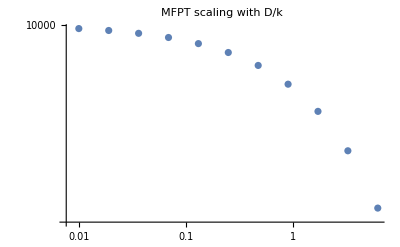

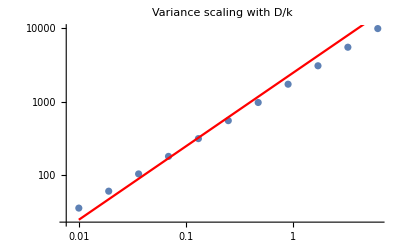

```mathematica
meandata = Thread[{DRange, Dmeans}]
vardata = Thread[{DRange, Dvar}] 
Show[ListLogLogPlot[meandata, PlotLabel-> "MFPT scaling with D/k"]](*, LogLogPlot[x0Constant/v, {v, 0, 0.0256}]]*)
Show[ListLogLogPlot[vardata, PlotLabel-> "Variance scaling with D/k" ],LogLogPlot[D/(4*kConstant*vConstant^2), {D,0.01, 10}, PlotStyle->Red, PlotLegends->"Slope = 1"]](*, LogLogPlot[DConstant/(8*kConstant*x^2), {x, 0, 0.0128}]]*)
```

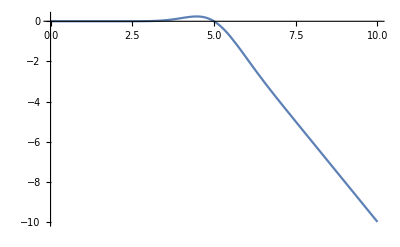

```mathematica
Plot[{(5-t)*Erfc[5-t]}, {t, 0, 10}, PlotLegends->"Expressions"]
```

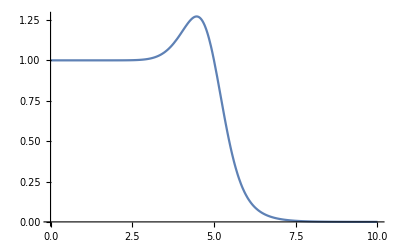

```mathematica
Plot[{Exp[(5-t)*Erfc[5-t]]}, {t, 0, 10}, PlotLegends->"Expressions"]
```